# Опыт Франка Герца

## Теоретическое введение

Опыт Франка-Герца – простой опыт, подтверждающий дискретность внутренней энергии атома. 
Разреженный одноатомный газ (He) заполняет трёхэлектродную лампу. Электроны, испускаемые разогретым катодом, ускоряются в постоянном электрическом поле, созданным между катодом и сетчатым анодом лампы. Передвигаясь от катода к аноду, электроны сталкиваются с атомами гелия. Если энергия электрона недостаточна для того, чтобы перевести его в возбужденное состояние (или ионизировать), то возможны только упругие столкновения. По мере увеличения разности потенциалов энергия электронов увеличивается и оказывается достаточной для возбуждения атомов. При таких неупругих столкновениях кинетическая энергия электрона передаётся одному из атомных электронов, вызывая его переход на свободный энергетический уровень (возбуждение) или совсем отрывая его от атома (ионизация).

Третьим электродом лампы является коллектор.Между ним и анодом поддерживается небольшое задерживающее напряжение.Ток коллектора измеряется микроамперметром.При увеличении потенциала анода ток в лампе вначале растет, а когда энергия электронов становится достаточной для возбуждения атомов, ток коллектора резко уменьшается, так как электроны почти полностью теряют свою энергию при неупругих соударениях с атомами.При дальнейшем увеличении потенциала анода ток коллектора вновь возрастает.Следующее замедление роста тока происходит в момент, когда часть электронов неупруго сталкивается с атомами два раза : первый раз посередине пути, второй-- у анода.Таким образом, на кривой зависимости тока коллектора от напряжения анода имеется ряд максимумов и минимумов, отстоящих друг от друга на равные расстояния $\Delta V$, равные энергии первого возбуждённого состояния.Теория, описывающая дискретность энергетических уровней атома He довольно сложная в плане вычислений, а концептуально всё сводится к решению уравнения Шрёдингера.

Гамильтониан системы выглядит следующим образом

Ĥ=-ℏ^2/(2m)Δ_1- ℏ^2/(2m)Δ_2- (Z e^2)/(4π ϵ r_1)- (Z e^2)/(4π ϵ r_2)+e^2/(4π ϵ r_12)

Решить требуется стационарное уравнение Шрёдингера

Ĥ Ψ(r_1,r_2)=E ψ(r_1,r_2)

Гамильтониан можно переписать в виде

Ĥ=(Ĥ)_1+(Ĥ)_2+v_12

где V_12 описывает взаимодействие электронов, которым традиционно пренебрегают, разделяют переменные и решают одноэлектронные уравнения Шрёдингера, получая приблизительную волновую функцию, затем используя соображения о принципе запрета Паули и т.д.учитывают спин электронов и делают поправки на их взаимодействие.Описание этой процедуры выходит за рамки работы, поэтому нет нужды описывать её подробно.

## Экспериментальная часть

Сначала исследуем ВАХ в динамическом режиме.Для трех значений задерживающего напряжения получим осциллограммы.Важно заметить, что развертка осуществляется справа налево.Цена деления осциллографа 5В.

-Graphics--Graphics--Graphics-

Затем, исследуем ВАХ более подробно, перейдя в статический режим.

Получение ВАХ I_k=f(V_a) в статистическом режиме измерений.

4 вольта

```mathematica
Voltage4=({{1, 2, 1.5}, {2, 4, 2.67}, {3, 6, 3.68}, {4, 8, 4.95}, {5, 10, 6.08}, {6, 12, 7.15}, {7, 14, 8.23}, {8, 16, 9.15}, {9, 18, 10.02}, {10, 20, 10.67}, {11, 22, 11.60}, {12, 24, 12.37}, {13, 26, 13.29}, {14, 28, 14.16}, {15, 30, 14.90}, {16, 32, 15.81}, {17, 34, 16.79}, {18, 36, 17.56}, {19, 38, 18.60}, {19.5, 38, 24.74}, {20, 40, 19.12}, {21, 42, 21.33}, {22, 44, 27.60}, {21.5, 45, 23.08}, {23, 46, 28.19}, {24, 48, 28.95}, {25, 50, 29.55}, {26, 52, 30.37}, {27, 54, 31.10}, {28, 56, 31.67}, {29, 58, 32.50}, {30, 60, 33.40}, {31, 62, 33.88}, {32.5, 62, 40.95}, {32, 64, 35.03}, {33, 66, 51.71}, {34, 68, 54.09}, {35, 70, 55.55}, {36, 72, 57.12}, {37, 74, 61.15}, {38, 76, 69.02}});
For[i=1,i<=Length[Voltage4],i++,
Voltage4[[i,1]]=i;
]
Grid[Voltage4,Dividers->All]
```

1 | 2 | 1.5
2 | 4 | 2.67
3 | 6 | 3.68
4 | 8 | 4.95
5 | 10 | 6.08
6 | 12 | 7.15
7 | 14 | 8.23
8 | 16 | 9.15
9 | 18 | 10.02
10 | 20 | 10.67
11 | 22 | 11.6
12 | 24 | 12.37
13 | 26 | 13.29
14 | 28 | 14.16
15 | 30 | 14.9
16 | 32 | 15.81
17 | 34 | 16.79
18 | 36 | 17.56
19 | 38 | 18.6
20 | 38 | 24.74
21 | 40 | 19.12
22 | 42 | 21.33
23 | 44 | 27.6
24 | 45 | 23.08
25 | 46 | 28.19
26 | 48 | 28.95
27 | 50 | 29.55
28 | 52 | 30.37
29 | 54 | 31.1
30 | 56 | 31.67
31 | 58 | 32.5
32 | 60 | 33.4
33 | 62 | 33.88
34 | 62 | 40.95
35 | 64 | 35.03
36 | 66 | 51.71
37 | 68 | 54.09
38 | 70 | 55.55
39 | 72 | 57.12
40 | 74 | 61.15
41 | 76 | 69.02

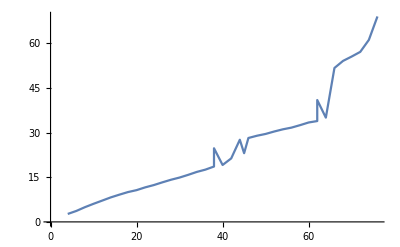

```mathematica
ListLinePlot[Voltage4[[2;;All,2;;3]]]
```

6 вольт

```mathematica
Voltage6=({{1, 2.69, 2}, {2, 4.25, 4}, {3, 6.16, 7}, {4, 8.08, 11}, {5, 10.10, 15}, {6, 12.24, 20}, {7, 14.13, 25}, {8, 16.33, 30}, {9, 18.34, 35}, {10, 20.33, 39}, {11, 22.30, 41}, {12, 24.29, 28}, {13, 26.44, 27}, {14, 28.30, 33}, {15, 30.03, 38}, {16, 32.75, 47}, {17, 34.60, 52}, {18, 36.59, 54}, {19, 38.77, 55}, {20, 40.40, 53}, {21, 42.50, 50}, {22, 44.42, 48}, {23, 46.39, 47}, {24, 48.60, 47}, {25, 50.68, 48}, {26, 52.01, 49}, {27, 54.31, 51}, {28, 56.33, 53}, {29, 58.49, 55}, {30, 60.79, 56}, {31, 62.35, 57}, {32, 64.44, 56}, {33, 68.15, 57}});
Grid[Voltage6,Dividers->All]
```

1 | 2.69 | 2
2 | 4.25 | 4
3 | 6.16 | 7
4 | 8.08 | 11
5 | 10.1 | 15
6 | 12.24 | 20
7 | 14.13 | 25
8 | 16.33 | 30
9 | 18.34 | 35
10 | 20.33 | 39
11 | 22.3 | 41
12 | 24.29 | 28
13 | 26.44 | 27
14 | 28.3 | 33
15 | 30.03 | 38
16 | 32.75 | 47
17 | 34.6 | 52
18 | 36.59 | 54
19 | 38.77 | 55
20 | 40.4 | 53
21 | 42.5 | 50
22 | 44.42 | 48
23 | 46.39 | 47
24 | 48.6 | 47
25 | 50.68 | 48
26 | 52.01 | 49
27 | 54.31 | 51
28 | 56.33 | 53
29 | 58.49 | 55
30 | 60.79 | 56
31 | 62.35 | 57
32 | 64.44 | 56
33 | 68.15 | 57

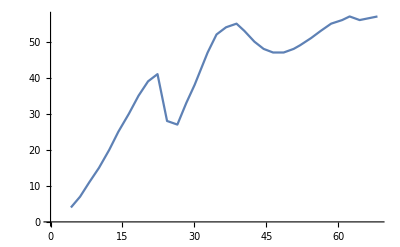

```mathematica
ListLinePlot[Voltage6[[2;;All,2;;3]]]
```

8 Вольт

```mathematica
Voltage8=({{1, 2.97, 0}, {2, 4.29, 1}, {3, 6.37, 4}, {4, 8.34, 8}, {5, 10.08, 11}, {6, 12.55, 17}, {7, 14.48, 22}, {8, 16.01, 25}, {9, 18.31, 30}, {10, 20.70, 35}, {11, 22.90, 39}, {12, 24.46, 40}, {13, 26.20, 17}, {14, 28.25, 19}, {15, 30.32, 25}, {16, 32.33, 32}, {17, 34.28, 38}, {18, 36.37, 42}, {19, 38.07, 44}, {20, 40.17, 42}, {21, 42.58, 40}, {22, 44.17, 38}, {23, 46.14, 35}, {24, 48.47, 33}, {25, 50.32, 33}, {26, 52.38, 34}, {27, 54.37, 36}, {28, 56.56, 38}, {29, 58.79, 39}, {30, 62.41, 40}, {31, 64.60, 40}, {32, 65.06, 40}, {33, 68.28, 39}, {34, 68.50, 39}});
Grid[Voltage8,Dividers->All]
```

1 | 2.97 | 0
2 | 4.29 | 1
3 | 6.37 | 4
4 | 8.34 | 8
5 | 10.08 | 11
6 | 12.55 | 17
7 | 14.48 | 22
8 | 16.01 | 25
9 | 18.31 | 30
10 | 20.7 | 35
11 | 22.9 | 39
12 | 24.46 | 40
13 | 26.2 | 17
14 | 28.25 | 19
15 | 30.32 | 25
16 | 32.33 | 32
17 | 34.28 | 38
18 | 36.37 | 42
19 | 38.07 | 44
20 | 40.17 | 42
21 | 42.58 | 40
22 | 44.17 | 38
23 | 46.14 | 35
24 | 48.47 | 33
25 | 50.32 | 33
26 | 52.38 | 34
27 | 54.37 | 36
28 | 56.56 | 38
29 | 58.79 | 39
30 | 62.41 | 40
31 | 64.6 | 40
32 | 65.06 | 40
33 | 68.28 | 39
34 | 68.5 | 39

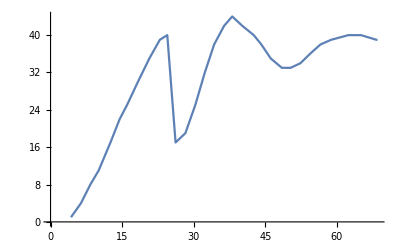

```mathematica
ListLinePlot[Voltage8[[2;;All,2;;3]]]
```

Сведем все графики на один лист

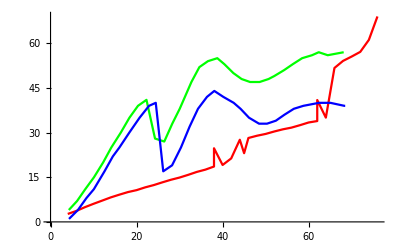

```mathematica
Show[ListLinePlot[Voltage4[[2;;All,2;;3]],PlotStyle->Red],ListLinePlot[Voltage6[[2;;All,2;;3]],PlotStyle->Green],ListLinePlot[Voltage8[[2;;All,2;;3]],PlotStyle->Blue]]
```

Вынесем разности напряжений между максимумами и минимумами в таблицу:

```mathematica
Voltages={Voltage4,Voltage6,Voltage8};
statMode=({{"U, V", "V_max1", "V_max2", "ΔV_max", "V_min1", "V_min2", "ΔV_min"}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}});
For[i=2,i≤ 4,i++,
statMode[[i,1]]=i*2;
MapMax=PeakDetect[Voltages[[i-1]][[All,3]]];
MapMin=PeakDetect[-Voltages[[i-1]][[All,3]]];
MaxS=DeleteCases[MapThread[And,{Voltages[[i-1]],MapMax/.{1->True,0->False}}],False];
MinS=DeleteCases[MapThread[And,{Voltages[[i-1]],MapMin/.{1->True,0->False}}],False];
For[j=1,j≤ Length[MaxS],j++,
If[(MaxS[[j,2]]<15) || (MaxS[[j,2]]>55),
Delete[MaxS,j];
];
];
For[l=1,l≤ Length[MinS],l++,
If[(MinS[[l,2]]<15)||(MinS[[l,2]]>55),
Delete[MinS,l];
];
];
statMode[[i,2]]=MaxS[[2]][[2]];
statMode[[i,3]]=MaxS[[3]][[2]];
statMode[[i,4]]=statMode[[i,3]]-statMode[[i,2]];
statMode[[i,5]]=MinS[[2]][[2]];
statMode[[i,6]]=MinS[[3]][[2]];
statMode[[i,7]]=statMode[[i,6]]-statMode[[i,5]];
];
Grid[statMode]
```

U, V | V_max1 | V_max2 | ΔV_max | V_min1 | V_min2 | ΔV_min
4 | 44 | 76 | 32 | 40 | 45 | 5
6 | 38.77 | 62.35 | 23.58 | 26.44 | 46.39 | 19.95
8 | 38.07 | 62.41 | 24.34 | 26.2 | 48.47 | 22.27

```mathematica
TeXForm[Voltage8]
```

\left(
\begin{array}{ccc}
 1 & 2.97 & 0 \\
 2 & 4.29 & 1 \\
 3 & 6.37 & 4 \\
 4 & 8.34 & 8 \\
 5 & 10.08 & 11 \\
 6 & 12.55 & 17 \\
 7 & 14.48 & 22 \\
 8 & 16.01 & 25 \\
 9 & 18.31 & 30 \\
 10 & 20.7 & 35 \\
 11 & 22.9 & 39 \\
 12 & 24.46 & 40 \\
 13 & 26.2 & 17 \\
 14 & 28.25 & 19 \\
 15 & 30.32 & 25 \\
 16 & 32.33 & 32 \\
 17 & 34.28 & 38 \\
 18 & 36.37 & 42 \\
 19 & 38.07 & 44 \\
 20 & 40.17 & 42 \\
 21 & 42.58 & 40 \\
 22 & 44.17 & 38 \\
 23 & 46.14 & 35 \\
 24 & 48.47 & 33 \\
 25 & 50.32 & 33 \\
 26 & 52.38 & 34 \\
 27 & 54.37 & 36 \\
 28 & 56.56 & 38 \\
 29 & 58.79 & 39 \\
 30 & 62.41 & 40 \\
 31 & 64.6 & 40 \\
 32 & 65.06 & 40 \\
 33 & 68.28 & 39 \\
 34 & 68.5 & 39 \\
\end{array}
\right)

```mathematica
For[i=1,i≤Length[Voltage8],i++,
Print["\t\t\t(",Voltage8[[i,2]],", ",Voltage8[[i,3]],")+-(0.5,0.5)"]
]
```

(2.97, 0)+-(0.5,0.5)

(4.29, 1)+-(0.5,0.5)

(6.37, 4)+-(0.5,0.5)

(8.34, 8)+-(0.5,0.5)

(10.08, 11)+-(0.5,0.5)

(12.55, 17)+-(0.5,0.5)

(14.48, 22)+-(0.5,0.5)

(16.01, 25)+-(0.5,0.5)

(18.31, 30)+-(0.5,0.5)

(20.7, 35)+-(0.5,0.5)

(22.9, 39)+-(0.5,0.5)

(24.46, 40)+-(0.5,0.5)

(26.2, 17)+-(0.5,0.5)

(28.25, 19)+-(0.5,0.5)

(30.32, 25)+-(0.5,0.5)

(32.33, 32)+-(0.5,0.5)

(34.28, 38)+-(0.5,0.5)

(36.37, 42)+-(0.5,0.5)

(38.07, 44)+-(0.5,0.5)

(40.17, 42)+-(0.5,0.5)

(42.58, 40)+-(0.5,0.5)

(44.17, 38)+-(0.5,0.5)

(46.14, 35)+-(0.5,0.5)

(48.47, 33)+-(0.5,0.5)

(50.32, 33)+-(0.5,0.5)

(52.38, 34)+-(0.5,0.5)

(54.37, 36)+-(0.5,0.5)

(56.56, 38)+-(0.5,0.5)

(58.79, 39)+-(0.5,0.5)

(62.41, 40)+-(0.5,0.5)

(64.6, 40)+-(0.5,0.5)

(65.06, 40)+-(0.5,0.5)

(68.28, 39)+-(0.5,0.5)

(68.5, 39)+-(0.5,0.5)

```mathematica
Grid[statMode]
```

U, V | V_max1 | V_max2 | ΔV_max | V_min1 | V_min2 | ΔV_min
4 | 44 | 76 | 32 | 40 | 45 | 5
6 | 38.77 | 62.35 | 23.58 | 26.44 | 46.39 | 19.95
8 | 38.07 | 62.41 | 24.34 | 26.2 | 48.47 | 22.27